## Illustration of concavity of specific flux using Harmonic Mean of enzymes as surrogate

## Fig 2A from main text.

## We use 1/(sum(1/e_i) instead of J(e)/e_T . First we show the surface on the (e1, e2)-simplex, using e1+e2+e3=1, create level sets and project these onto the triangle 0 <= e1 + e2 <= 1for comparison.

```mathematica
Clear["Global`*"]
SetOptions[{ContourPlot,Plot3D,ParametricPlot,Plot,ListLinePlot,ListPlot},BaseStyle->{FontSize->16,FontColor->Black},ImageSize->600,PlotRange->All];
SetOptions[{ParametricPlot,Plot,ListLinePlot,ListPlot},PlotStyle->(Directive[AbsoluteThickness[3],#]&/@ColorData[68,"ColorList"]),Frame->False,FrameStyle-> Thickness[0.002],BaseStyle->{FontSize->16,FontColor->Black}];
padding={{40,30},{20,20}};
```

```mathematica
g = e1 e2 e3/(e1 e2 + e2 e3 + e1 e3)/.{e3->1-e1-e2}
cp2=ContourPlot[g,{e1,0,1},{e2,0,1-e1},Frame->False,Axes->False,PlotRangePadding->0,Contours->Table[0.01 + 0.02 j,{j,1,5}],ContourShading->False,ContourLabels->None,ContourStyle->{{Thickness[.01],Red}}];
p1=Plot3D[g,{e1,0,1},{e2,0,1-e1},
MeshFunctions->(#3&),
Mesh->{Table[{0.01 + 0.02 j},{j,1,5}]},
BoxRatios->{2,1.2,1.2},
MeshStyle->{Thick,Red},
PlotStyle->Opacity[0.2],
ViewPoint->1000{-0.7,-1,0.6},
ViewVertical->{0,0,1},
ViewAngle->0.001,
ImagePadding->padding];
level=-1.2 10^-8;gr=Graphics3D[{Texture[cp2],EdgeForm[],Polygon[{{0,0,level},{0,1,level},{1,0,level}},VertexTextureCoordinates->{{0,0},{1,0},{0,1}}]},Lighting->"Neutral",ImagePadding->padding];
Show[p1,gr]
Export["/Users/rplanque/Documents/GitHub/qORAC2/pics/qORAC_concave.jpg",Show[p1,gr],ImageResolution->300];
```

(e1 (1-e1-e2) e2)/(e1 (1-e1-e2)+e1 e2+(1-e1-e2) e2)

-Graphics3D-

## Figure 2B from main text

## the functions used here are again just for illustrative purposes

(e1^0.8 e2^1.2 (1-e1^0.8-e2^1.2))/(e1^0.8 e2^1.2+e1^0.8 (1-e1^0.8-e2^1.2)+e2^1.2 (1-e1^0.8-e2^1.2))

(e1 (1-e1-e2) e2)/(e1 (1-e1-e2)+e1 e2+(1-e1-e2) e2)

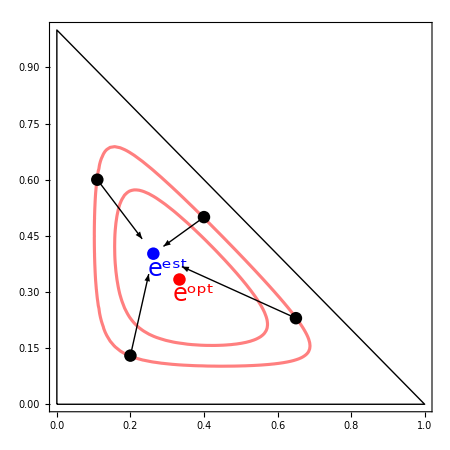

/Users/rplanque/Documents/GitHub/qORAC2/pics/qORAC_levelsets_2.jpg

```mathematica
g = e1 e2 e3/(e1 e2 + e2 e3 + e1 e3)/.{e1->e1^0.8,e2->e2^1.2}/.{e3->1-e1^0.8-e2^1.2}
cp1=ContourPlot[g,{e1,0,1},{e2,0,1-e1},Axes->True,Contours->Table[0.01+0.040015 j,{j,1,3}],ContourShading->False,ContourLabels->None,ContourStyle->{{Thickness[.003],Blue}},PlotPoints->20
];
g = e1 e2 e3/(e1 e2 + e2 e3 + e1 e3)/.{e1->e1,e2->e2}/.{e3->1-e1-e2}
cp2=ContourPlot[g,{e1,0,1},{e2,0,1-e1},Axes->True,
Contours->Table[0.01 + 0.02 j,{j,3,4}],ContourShading->False,ContourLabels->None,ContourStyle->{{Thickness[.005],Red}},PlotPoints->20,ImageSize->450,FrameStyle->Directive[Black,24,Thickness->0.005,PlotTheme->"Marketing"]];
pol=Graphics[Line[{{0,0},{1,0},{0,1},{0,0}}],AxesLabel->{e1,e2}];
point=Graphics[{PointSize[0.02],Red,Point[{1/3,1/3}],Text[Style[Superscript[e,opt],FontSize->24],{1/3+0.04,1/3-0.04}]}];

maxsol=Maximize[{ e1 e2 e3/(e1 e2 + e2 e3 + e1 e3)/.{e1->e1^0.8,e2->e2^1.2},0≤e1≤1,0≤e2≤1,0≤e3≤1,e1+e2+e3==1},{e1,e2,e3}];
e1max = e1/.maxsol[[2,1]];
e2max = e2/.maxsol[[2,2]];
point2=Graphics[{PointSize[0.02],Blue,Point[{e1max,e2max}],Text[Style[Superscript[e,est],FontSize->24],{e1max+0.04,e2max-0.04}]}];

stpoint={0.2,0.13};
pointe1=Graphics[{PointSize[.02],Black,Point[stpoint]}];
endpoint = {e1max,e2max} - 0.2 {e1max - stpoint[[1]],e2max-stpoint[[2]]};
arrow1=Graphics[Arrow[{stpoint,endpoint}]];

stpoint={0.4,0.5};
pointe2=Graphics[{PointSize[.02],Black,Point[stpoint]}];
endpoint = {e1max,e2max} - 0.2 {e1max - stpoint[[1]],e2max-stpoint[[2]]};
arrow2=Graphics[Arrow[{stpoint,endpoint}]];

stpoint={0.11,0.6};
pointe3=Graphics[{PointSize[.02],Black,Point[stpoint]}];
endpoint = {e1max,e2max} - 0.2 {e1max - stpoint[[1]],e2max-stpoint[[2]]};
arrow3=Graphics[Arrow[{stpoint,endpoint}]];

stpoint={0.65,0.23};
pointe4=Graphics[{PointSize[.02],Black,Point[stpoint]}];
endpoint = {e1max,e2max} - 0.2 {e1max - stpoint[[1]],e2max-stpoint[[2]]};
arrow4=Graphics[Arrow[{stpoint,endpoint}]];

Show[cp2,pol,point,point2,pointe1,arrow1, pointe2,arrow2,pointe3,arrow3,pointe4,arrow4 ,Frame-> True]

Export["/Users/rplanque/Documents/GitHub/qORAC2/pics/qORAC_levelsets_2.jpg",Show[cp2,pol,point,point2,pointe1,arrow1, pointe2,arrow2,pointe3,arrow3,pointe4,arrow4,Frame-> True],ImageResolution->300]
```

## Figure 3 from main text

/Users/rplanque/Documents/SystemsBiology/qORAC2/qORAC_Fz.jpg

{{e1→0.392375},{e1→1.27429}}

{0.264076}

0.16

0.238417

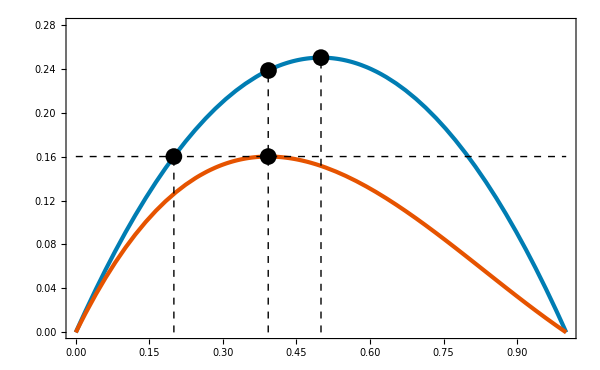

/Users/rplanque/Documents/GitHub/qORAC2/pics/qORAC_control.jpg

```mathematica
f1=e1(1-e1);
f2=e1(e1-1)(e1-1.5);
sols=Solve[D[f2,e1]==0,e1]
heightatmax=f2/.{sols[[1]]}
actualheight=f1/.{e1->0.2}
otherheight=f1/.sols[[1]]
factor=actualheight/heightatmax;

p1=Plot[{e1(1-e1),factor e1(e1-1)(e1-1.5)},{e1,0,1},FrameStyle->Directive[Black,18,Thickness->0.005,PlotTheme->"Marketing"],BaseStyle->{FontSize->18,FontColor->Black},Axes->{True,True},Frame->True,PlotRange->{{0,1},{0,0.28}}];
p2=Graphics[{PointSize[0.02],Black,Point[{0.2,actualheight}]}];
p3=Graphics[{PointSize[0.02],Black,Point[{e1/.sols[[1]],actualheight}]}];
p4=Graphics[{Dashed,Black,Line[{{0,actualheight},{1,actualheight}}]}];
p5=Graphics[{PointSize[0.02],Black,Point[{1/2,f1/.{e1->1/2}}]}];
p6=Graphics[{PointSize[0.02],Black,Point[{0.2,0}]}];
p7=Graphics[{PointSize[0.02],Black,Point[{e1/.sols[[1]],0}]}];
p8=Graphics[{Dashed,Black,Line[{{0.2,0},{0.2,actualheight}}]}];
p9=Graphics[{Dashed,Black,Line[{{1/2,0},{1/2,1/4}}]}];
p10=Graphics[{Dashed,Black,Line[{{e1/.sols[[1]],0},{e1/.sols[[1]],  otherheight}}]}];
p11=Graphics[Arrow[{{0.2,0},{0.35,0}}]];
p12=Graphics[{PointSize[0.02],Black,Point[{e1/.sols[[1]],otherheight}]}];

Show[p1,p2,p3,p4,p5,p8,p9,p10,p12]
Export["/Users/rplanque/Documents/GitHub/qORAC2/pics/qORAC_control.jpg",Show[p1,p2,p3,p4,p5,p8,p9,p10,p12],ImageResolution->300]
```

```mathematica
"/Users/rplanque/Documents/GitHub/qORAC2/pics/qORAC_control.jpg"
```

## Supplementary Fig 1.

{4.4,{z1→2.1,z2→2.3}}

{6.,{z1→2.9,z2→3.1}}

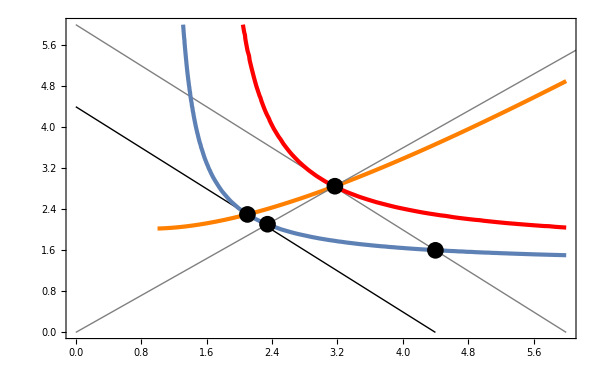

/Users/rplanque/Documents/GitHub/qORAC2/pics/qORAC_Fz.jpg

```mathematica
simplex=Graphics[Line[{{4.4,0},{0,4.4}}],Axes->True,Frame->True];
min = Minimize[{z1+z2,1/(z1-0.1)+1/(z2-0.3)==1,0<z1<4,0.3<z2<4},{z1,z2}]
min2 = Minimize[{z1+z2,1.4/(z1-0.1)+1.4/(z2-0.3)==1,0<z1<4,0.3<z2<4},{z1,z2}]
cntplot=ContourPlot[1/(z1-0.1)+1/(z2-0.3)==1,{z1,0.1,6},{z2,0.3,6},ContourStyle->{Thickness->0.005},Axes->True];

simplex2=Graphics[{Gray,Line[{{min2[[1]],0},{0,min2[[1]]}}]}];
cntplot2=ContourPlot[1.5/(z1-0.1)+1.3/(z2-0.3)==1,{z1,0.1,6},{z2,0.3,6},ContourStyle->{Red,Thickness->0.005},Axes->True];

pt = Graphics[{PointSize[0.02],Black,Point[{z1/.min[[2,1]],z2/.min[[2,2]]}]}];
pt2=Graphics[{PointSize[0.02],Black,Point[{4.4,1.6}]}];
pt3=Graphics[{PointSize[0.02],Black,Point[{3.17,2.85}]}];
line2=Graphics[{Gray,Line[{{0,0},12{3.17,2.85}}]}];
pt4=Graphics[{PointSize[0.02],Black,Point[0.74{3.17,2.85}]}];
graph=Plot[(x-z1/.min[[2,1]])x/(3+x)+z2/.min[[2,2]],{x,1,6},PlotStyle->{Orange,Thickness->0.005},FrameStyle->Directive[Black,18,Thickness->0.005,PlotTheme->"Marketing"],BaseStyle->{FontSize->18,FontColor->Black},Axes->{False,False},Frame->True,PlotRange->{{0,6},{0,6}}];
Show[graph,simplex,simplex2,line2,cntplot,cntplot2,pt,pt2,pt3,pt4]
Export["/Users/rplanque/Documents/GitHub/qORAC2/pics/qORAC_Fz.jpg",Show[graph,simplex,simplex2,line2,cntplot,cntplot2,pt,pt2,pt3,pt4],ImageResolution->300]
```

## Supplementary Fig 2

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLinePlot,ListLinePlot},PlotStyle->Black,Frame->True,ImageSize->500,BaseStyle->{FontSize->36,FontColor->Black},FrameStyle->Directive[Black,24,Thickness->0.005,PlotTheme->"Marketing"]
,PlotMarkers->Graphics[{EdgeForm[Directive[Thick,Black]],Disk[]},ImageSize->16], PlotStyle->{ColorData[68,"ColorList"],Thickness[0.01]},AspectRatio->0.75,ImagePadding->padding];
```

(e1^1.1 (1-e1^1.1-e2^0.9) e2^0.9)/(e1^1.1 (1-e1^1.1-e2^0.9)+e1^1.1 e2^0.9+(1-e1^1.1-e2^0.9) e2^0.9)

(e1 (1-e1-e2) e2)/(e1 (1-e1-e2)+e1 e2+(1-e1-e2) e2)

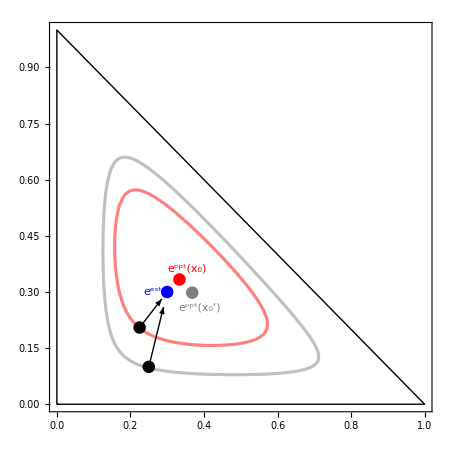

/Users/rplanque/Documents/GitHub/qORAC2/pics/qORAC_levelsets_4.jpg

```mathematica
g = e1 e2 e3/(e1 e2 + e2 e3 + e1 e3)/.{e1->e1^1.1,e2->e2^0.9}/.{e3->1-e1^1.1-e2^0.9}
cp1=ContourPlot[g,{e1,0,1},{e2,0,1-e1},Axes->True,Contours->Table[0.01+0.02 j,{j,3,3}],ContourShading->False,ContourLabels->None,ContourStyle->{{Thickness[.005],Gray}},PlotPoints->20,ImageSize->450,FrameStyle->Directive[Black,24,Thickness->0.005,PlotTheme->"Marketing"]
];
g = e1 e2 e3/(e1 e2 + e2 e3 + e1 e3)/.{e1->e1,e2->e2}/.{e3->1-e1-e2}
cp2=ContourPlot[g,{e1,0,1},{e2,0,1-e1},
Contours->Table[0.01 + 0.02 j,{j,4,4}],ContourShading->False,ContourLabels->None,ContourStyle->{{Thickness[.005],Red}},PlotPoints->20];
pol=Graphics[Line[{{0,0},{1,0},{0,1},{0,0}}],AxesLabel->{e1,e2}];
point=Graphics[{PointSize[0.02],Red,Point[{1/3,1/3}],Text["e^opt(x_0)",{1/3+0.02,1/3+0.03}]}];

maxsol=Maximize[{ e1 e2 e3/(e1 e2 + e2 e3 + e1 e3)/.{e1->e1^1.1,e2->e2^0.9},0≤e1≤1,0≤e2≤1,0≤e3≤1,e1+e2+e3==1},{e1,e2,e3}];
e1max = e1/.maxsol[[2,1]];
e2max = e2/.maxsol[[2,2]];
point2=Graphics[{PointSize[0.02],Gray,Point[{e1max,e2max}],Text["e^opt(x_0')",{e1max+0.02,e2max-0.04}]}];

e1max = 0.3;
e2max = 0.3;
point3=Graphics[{PointSize[0.02],Blue,Point[{e1max,e2max}],Text[Superscript[e,est],{e1max-0.04,e2max-0.0}]}];

stpoint={0.225,0.205};
pointe1=Graphics[{PointSize[.02],Black,Point[stpoint]}];
endpoint = {e1max,e2max} - 0.2 {e1max - stpoint[[1]],e2max-stpoint[[2]]};
arrow1=Graphics[Arrow[{stpoint,endpoint}]];

stpoint={0.25,0.1};
pointe2=Graphics[{PointSize[.02],Black,Point[stpoint]}];
endpoint = {e1max,e2max} - 0.2 {e1max - stpoint[[1]],e2max-stpoint[[2]]};
arrow2=Graphics[Arrow[{stpoint,endpoint}]];
Show[cp1,cp2,pol,point,point2,point3,pointe1,arrow1,pointe2,arrow2,Frame-> True ]

Export["/Users/rplanque/Documents/GitHub/qORAC2/pics/qORAC_levelsets_4.jpg",Show[cp1,cp2,pol,point,point2,point3,pointe1,arrow1,pointe2,arrow2, Frame-> True],ImageResolution->300]
```

## Unpublished figure, showing that enzyme allocations on a different flux level set give a different estimated optimal allocation

(e1^1.2 (1-e1^1.2-e2^0.7) e2^0.7)/(e1^1.2 (1-e1^1.2-e2^0.7)+e1^1.2 e2^0.7+(1-e1^1.2-e2^0.7) e2^0.7)

(e1 (1-e1-e2) e2)/(e1 (1-e1-e2)+e1 e2+(1-e1-e2) e2)

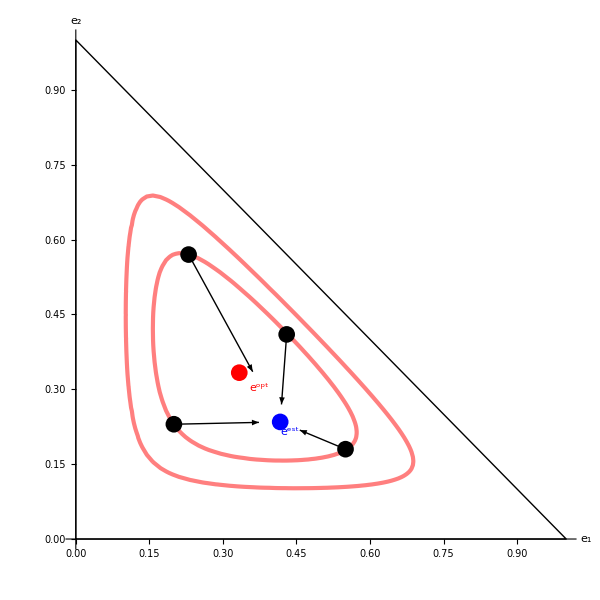

/Users/rplanque/Documents/GitHub/qORAC2/pics/qORAC_levelsets_3.jpg

```mathematica
g = e1 e2 e3/(e1 e2 + e2 e3 + e1 e3)/.{e1->e1^1.2,e2->e2^0.7}/.{e3->1-e1^1.2-e2^0.7}
cp1=ContourPlot[g,{e1,0,1},{e2,0,1-e1},Axes->True,AxesLabel->{Subscript[e, 1],Subscript[e, 2]},Contours->Table[0.01+0.040015 j,{j,1,3}],ContourShading->False,ContourLabels->None,ContourStyle->{{Thickness[.003],Blue}},PlotPoints->20
];
g = e1 e2 e3/(e1 e2 + e2 e3 + e1 e3)/.{e1->e1,e2->e2}/.{e3->1-e1-e2}
cp2=ContourPlot[g,{e1,0,1},{e2,0,1-e1},Axes->True,AxesLabel->{Subscript[e, 1],Subscript[e, 2]},
Contours->Table[0.01 + 0.02 j,{j,3,4}],ContourShading->False,ContourLabels->None,ContourStyle->{{Thickness[.005],Red}},PlotPoints->20];
pol=Graphics[Line[{{0,0},{1,0},{0,1},{0,0}}],AxesLabel->{e1,e2}];
point=Graphics[{PointSize[0.02],Red,Point[{1/3,1/3}],Text[Superscript[e,opt],{1/3+0.04,1/3-0.03}]}];

maxsol=Maximize[{ e1 e2 e3/(e1 e2 + e2 e3 + e1 e3)/.{e1->e1^1.2,e2->e2^0.7},0≤e1≤1,0≤e2≤1,0≤e3≤1,e1+e2+e3==1},{e1,e2,e3}];
e1max = e1/.maxsol[[2,1]];
e2max = e2/.maxsol[[2,2]];
point2=Graphics[{PointSize[0.02],Blue,Point[{e1max,e2max}],Text[Superscript[e,est],{e1max+0.02,e2max-0.02}]}];

stpoint={0.2,0.23};
pointe1=Graphics[{PointSize[.02],Black,Point[stpoint]}];
endpoint = {e1max,e2max} - 0.2 {e1max - stpoint[[1]],e2max-stpoint[[2]]};
arrow1=Graphics[Arrow[{stpoint,endpoint}]];

stpoint={0.43,0.41};
pointe2=Graphics[{PointSize[.02],Black,Point[stpoint]}];
endpoint = {e1max,e2max} - 0.2 {e1max - stpoint[[1]],e2max-stpoint[[2]]};
arrow2=Graphics[Arrow[{stpoint,endpoint}]];

stpoint={0.23,0.57};
pointe3=Graphics[{PointSize[.02],Black,Point[stpoint]}];
endpoint = {e1max,e2max} - 0.3 {e1max - stpoint[[1]],e2max-stpoint[[2]]};
arrow3=Graphics[Arrow[{stpoint,endpoint}]];

stpoint={0.55,0.18};
pointe4=Graphics[{PointSize[.02],Black,Point[stpoint]}];
endpoint = {e1max,e2max} - 0.3 {e1max - stpoint[[1]],e2max-stpoint[[2]]};
arrow4=Graphics[Arrow[{stpoint,endpoint}]];

Show[cp2,pol,point,point2,pointe1,arrow1, pointe2,arrow2,pointe3,arrow3,pointe4,arrow4,Frame-> False ]

Export["/Users/rplanque/Documents/GitHub/qORAC2/pics/qORAC_levelsets_3.jpg",Show[cp2,pol,point,point2,pointe1,arrow1, pointe2,arrow2,pointe3,arrow3,pointe4,arrow4,Frame-> False],ImageResolution->300]
```